```mathematica
Length[Select[IntegerDigits[2^1000,3],#==0&]]
```

213

```mathematica
Length[Select[IntegerDigits[2^1000,3],#==2&]]
```

224

```mathematica
Length[IntegerDigits[2^1000,3]]
```

631

```mathematica
Length[Select[IntegerDigits[2^1000,3],#==1&]]
```

194

```mathematica
MatrixForm[Table[MyLast[Flatten[Take[Reverse[IntegerDigits[2^i,3]],6],4]],{i,8,100,1}], TableDirections->Row]
```

(1 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1)

```mathematica
RepeatDigits[n_]:= RepeatDigits[n]=Module[{startPattern,  start = 0, current, digits, bad, tail, badList},
badList={};
digits = IntegerDigits[2^start, 3];
Print["Found sufficient length at " <> ToString[start]];
startPattern = Take[PadLeft[digits,n],-n];
Print["Start pattern " <> ToString[startPattern]];
current = start +1;
digits = IntegerDigits[2^current, 3];
tail = Take[PadLeft[digits,n],-n];
bad=0;
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current]];
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[2^current, 3];
tail = Take[PadLeft[digits,n],-n];
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current]];
];
Print["Found repeating pattern after " <> ToString[current- start]];
Print["Count without a 2 in it " <> ToString[bad]];
Print["Bad positions " <> ToString[badList]];
Return[badList]
]
```

```mathematica
RepeatDigits[12]
```

Found sufficient length at 0

Start pattern {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}

$Aborted

Found sufficient length at 8

Found repeating pattern after 486

Count without a 2 in it 32

Bad positions {20, 24, 26, 56, 62, 72, 74, 80, 126, 150, 162, 164, 186, 188, 216, 218, 240, 242, 258, 288, 332, 344, 378, 386, 396, 398, 402, 420, 474, 486, 488, 494}

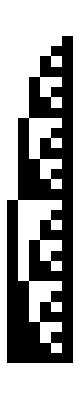

```mathematica
ArrayPlot[Sort[Map [Take[IntegerDigits[2^#,3],-6]&,RepeatDigits[6]]]]
```

Found sufficient length at 12

Found repeating pattern after 4374

Count without a 2 in it 128

Bad positions {24, 26, 72, 80, 126, 164, 186, 188, 218, 240, 242, 332, 378, 386, 474, 488, 494, 560, 566, 636, 648, 650, 728, 774, 864, 872, 882, 992, 1028, 1044, 1046, 1134, 1160, 1188, 1190, 1230, 1260, 1374, 1392, 1458, 1460, 1466, 1478, 1482, 1514, 1584, 1644, 1646, 1674, 1676, 1698, 1700, 1844, 1854, 1856, 1878, 1932, 1944, 1946, 1952, 2006, 2018, 2070, 2094, 2130, 2184, 2186, 2202, 2288, 2322, 2330, 2342, 2346, 2450, 2454, 2456, 2486, 2492, 2502, 2504, 2580, 2592, 2718, 2762, 2774, 2904, 2936, 2942, 2972, 2988, 2996, 3080, 3132, 3248, 3294, 3312, 3314, 3336, 3402, 3464, 3482, 3528, 3564, 3566, 3588, 3642, 3660, 3690, 3746, 3798, 3800, 3804, 3912, 3914, 3950, 4038, 4076, 4104, 4106, 4146, 4220, 4232, 4290, 4308, 4362, 4374, 4376, 4382}

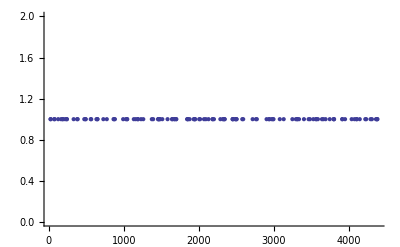

```mathematica
With[
{length=8},
ListPlot[
With[
{all=Map[{#,1}&,RepeatDigits[length]]},
all
]]
]
```

```mathematica
ListLinePlot[Table[RepeatDigits[pos], {pos,20,20}]]
```

Found sufficient length at 31

$Aborted

```mathematica
Limit[2^x / 3^x, x->Infinity]
```

0

```mathematica
RepeatDigitsHead[n_]:= Module[{startPattern,  start = 0, current, digits, bad, tail, badList},
badList={};
digits = IntegerDigits[2^start, 3];
While[Length[digits] < n,
start +=1;
digits = IntegerDigits[2^start, 3];
];
Print["Found sufficient length at " <> ToString[start]];
startPattern = Take[digits,n];
current = start +1;
digits = IntegerDigits[2^current, 3];
tail = Take[digits,-n];
bad=0;
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current]];
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[2^current, 3];
tail = Take[digits,n];
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current]];
];
Print["Found repeating pattern after " <> ToString[current- start]];
Print["Count without a 2 in it " <> ToString[bad]];
Print["Bad positions " <> ToString[badList]];
Return[badList]
]
```

```mathematica
TableForm[Table[{i,Length[RepeatDigitsHead[i]]},{i,1,8}]]
```

Found sufficient length at 0

Found repeating pattern after 2

Count without a 2 in it 1

Bad positions {2}

Found sufficient length at 2

Found repeating pattern after 5

Count without a 2 in it 2

Bad positions {5, 7}

Found sufficient length at 4

Found repeating pattern after 8

Count without a 2 in it 2

Bad positions {8, 10}

Found sufficient length at 5

Found repeating pattern after 46

Count without a 2 in it 10

Bad positions {8, 10, 18, 24, 27, 29, 37, 43, 46, 48}

Found sufficient length at 7

Found repeating pattern after 233

Count without a 2 in it 31

Bad positions {8, 24, 27, 29, 37, 43, 65, 67, 81, 83, 92, 108, 111, 113, 121, 127, 130, 146, 149, 151, 165, 167, 176, 192, 197, 205, 211, 214, 230, 233, 235}

Found sufficient length at 8

Found repeating pattern after 401

Count without a 2 in it 34

Bad positions {27, 29, 37, 43, 67, 83, 92, 108, 111, 113, 121, 127, 151, 192, 211, 233, 249, 276, 281, 289, 298, 314, 317, 319, 333, 335, 344, 365, 373, 382, 398, 401, 403, 409}

Found sufficient length at 10

Found repeating pattern after 2593

Count without a 2 in it 165

Bad positions {27, 43, 92, 108, 111, 113, 121, 151, 211, 276, 281, 289, 298, 317, 333, 335, 382, 398, 403, 417, 428, 449, 457, 466, 482, 485, 487, 493, 514, 522, 528, 550, 552, 566, 568, 596, 598, 606, 612, 636, 652, 661, 677, 696, 761, 802, 818, 845, 850, 858, 867, 883, 886, 888, 904, 913, 934, 942, 970, 972, 978, 986, 988, 997, 999, 1007, 1035, 1037, 1051, 1053, 1081, 1097, 1146, 1162, 1165, 1167, 1205, 1265, 1303, 1330, 1335, 1343, 1352, 1371, 1387, 1389, 1436, 1452, 1471, 1482, 1503, 1511, 1520, 1536, 1539, 1541, 1547, 1568, 1576, 1582, 1604, 1606, 1620, 1622, 1650, 1652, 1660, 1690, 1706, 1715, 1731, 1750, 1815, 1856, 1872, 1899, 1904, 1912, 1921, 1937, 1942, 1958, 1967, 1988, 1996, 2024, 2026, 2032, 2040, 2042, 2051, 2053, 2061, 2089, 2091, 2105, 2107, 2135, 2151, 2200, 2216, 2219, 2221, 2259, 2319, 2357, 2384, 2389, 2397, 2406, 2425, 2427, 2441, 2443, 2490, 2506, 2525, 2536, 2557, 2565, 2574, 2590, 2593, 2595, 2601}

Found sufficient length at 12

Found repeating pattern after 19457

Count without a 2 in it 819

Bad positions {27, 92, 108, 111, 113, 121, 151, 211, 276, 289, 333, 335, 382, 403, 417, 428, 457, 514, 522, 550, 552, 566, 568, 598, 606, 612, 636, 652, 661, 696, 802, 818, 845, 858, 867, 883, 886, 888, 904, 942, 970, 978, 997, 999, 1007, 1037, 1051, 1053, 1081, 1146, 1162, 1165, 1167, 1205, 1265, 1330, 1343, 1387, 1389, 1436, 1452, 1471, 1511, 1568, 1576, 1604, 1606, 1620, 1622, 1652, 1660, 1690, 1706, 1715, 1731, 1750, 1856, 1872, 1899, 1912, 1937, 1958, 1996, 2024, 2032, 2051, 2053, 2061, 2091, 2105, 2107, 2135, 2200, 2216, 2219, 2221, 2259, 2319, 2397, 2441, 2443, 2490, 2506, 2525, 2557, 2565, 2574, 2622, 2630, 2658, 2660, 2674, 2676, 2706, 2714, 2744, 2769, 2785, 2804, 2910, 2926, 2953, 2966, 2991, 3012, 3042, 3050, 3078, 3086, 3105, 3107, 3115, 3145, 3159, 3161, 3189, 3254, 3270, 3313, 3373, 3451, 3495, 3497, 3544, 3560, 3579, 3611, 3619, 3628, 3647, 3676, 3684, 3690, 3712, 3714, 3728, 3730, 3760, 3798, 3823, 3839, 3858, 3964, 3980, 4007, 4020, 4045, 4066, 4096, 4104, 4132, 4140, 4148, 4159, 4161, 4169, 4199, 4215, 4243, 4308, 4324, 4427, 4505, 4549, 4551, 4598, 4614, 4633, 4665, 4673, 4682, 4701, 4709, 4730, 4738, 4744, 4766, 4768, 4782, 4784, 4877, 4893, 4912, 5018, 5066, 5074, 5099, 5120, 5150, 5158, 5186, 5194, 5202, 5213, 5215, 5223, 5253, 5269, 5297, 5362, 5378, 5481, 5559, 5568, 5587, 5603, 5605, 5652, 5668, 5687, 5719, 5736, 5755, 5763, 5784, 5792, 5798, 5836, 5838, 5931, 5947, 5966, 6072, 6120, 6128, 6153, 6174, 6183, 6204, 6212, 6240, 6248, 6256, 6267, 6269, 6277, 6307, 6323, 6351, 6416, 6432, 6535, 6605, 6613, 6622, 6641, 6657, 6659, 6706, 6722, 6741, 6773, 6790, 6809, 6817, 6846, 6852, 6890, 6892, 6920, 6985, 7001, 7020, 7126, 7174, 7182, 7207, 7237, 7258, 7266, 7294, 7302, 7310, 7321, 7323, 7331, 7377, 7405, 7421, 7470, 7486, 7589, 7659, 7667, 7676, 7695, 7711, 7713, 7760, 7776, 7795, 7827, 7844, 7863, 7871, 7900, 7906, 7944, 7946, 7974, 8039, 8055, 8139, 8180, 8228, 8236, 8261, 8291, 8312, 8348, 8356, 8364, 8366, 8385, 8431, 8459, 8475, 8524, 8540, 8643, 8713, 8721, 8730, 8749, 8765, 8767, 8830, 8849, 8881, 8898, 8917, 8919, 8925, 8960, 9028, 9093, 9109, 9193, 9234, 9282, 9290, 9315, 9345, 9366, 9402, 9404, 9410, 9418, 9420, 9439, 9467, 9485, 9513, 9529, 9578, 9594, 9697, 9767, 9775, 9784, 9803, 9884, 9903, 9935, 9952, 9968, 9971, 9973, 9979, 10014, 10082, 10138, 10147, 10163, 10247, 10288, 10336, 10344, 10369, 10374, 10399, 10420, 10456, 10458, 10464, 10472, 10474, 10493, 10521, 10539, 10567, 10583, 10632, 10648, 10751, 10789, 10821, 10829, 10838, 10857, 10859, 10938, 10957, 10989, 11006, 11022, 11025, 11027, 11033, 11068, 11136, 11146, 11192, 11201, 11217, 11301, 11342, 11390, 11398, 11423, 11428, 11453, 11474, 11510, 11512, 11518, 11526, 11528, 11575, 11621, 11637, 11686, 11702, 11843, 11870, 11875, 11883, 11892, 11911, 11913, 11992, 12011, 12013, 12022, 12043, 12060, 12076, 12079, 12081, 12087, 12122, 12190, 12192, 12200, 12246, 12255, 12271, 12355, 12396, 12444, 12461, 12477, 12482, 12507, 12528, 12564, 12566, 12572, 12580, 12582, 12629, 12675, 12691, 12731, 12756, 12897, 12924, 12929, 12937, 12946, 12965, 12967, 13046, 13065, 13067, 13076, 13097, 13114, 13130, 13133, 13135, 13141, 13176, 13244, 13246, 13254, 13284, 13300, 13309, 13325, 13409, 13450, 13498, 13515, 13531, 13536, 13561, 13582, 13618, 13620, 13626, 13634, 13636, 13683, 13699, 13729, 13731, 13739, 13745, 13769, 13785, 13810, 13951, 13978, 13983, 13991, 14000, 14019, 14021, 14100, 14119, 14121, 14130, 14151, 14168, 14184, 14187, 14189, 14195, 14230, 14298, 14300, 14308, 14338, 14354, 14363, 14379, 14463, 14504, 14552, 14569, 14585, 14590, 14615, 14636, 14672, 14674, 14680, 14688, 14690, 14737, 14739, 14753, 14783, 14785, 14793, 14799, 14823, 14839, 14864, 14883, 15005, 15032, 15037, 15054, 15073, 15075, 15154, 15173, 15175, 15184, 15205, 15222, 15224, 15238, 15241, 15243, 15249, 15284, 15352, 15354, 15362, 15392, 15408, 15417, 15433, 15517, 15558, 15574, 15606, 15623, 15639, 15644, 15669, 15690, 15698, 15726, 15728, 15734, 15742, 15744, 15755, 15791, 15793, 15807, 15837, 15839, 15847, 15853, 15877, 15893, 15918, 15937, 16059, 16086, 16091, 16108, 16127, 16129, 16208, 16227, 16229, 16238, 16259, 16276, 16278, 16292, 16295, 16297, 16303, 16338, 16406, 16408, 16416, 16446, 16462, 16471, 16487, 16571, 16612, 16628, 16660, 16677, 16698, 16723, 16744, 16752, 16780, 16782, 16788, 16796, 16798, 16809, 16845, 16847, 16861, 16891, 16893, 16901, 16907, 16931, 16947, 16991, 17113, 17140, 17145, 17162, 17181, 17183, 17199, 17262, 17281, 17283, 17292, 17294, 17313, 17330, 17332, 17346, 17349, 17351, 17357, 17392, 17441, 17460, 17462, 17470, 17500, 17516, 17525, 17541, 17560, 17625, 17666, 17682, 17714, 17731, 17752, 17777, 17798, 17806, 17836, 17842, 17850, 17852, 17863, 17899, 17901, 17915, 17945, 17947, 17955, 17961, 17985, 18001, 18045, 18167, 18194, 18199, 18216, 18235, 18237, 18253, 18291, 18316, 18335, 18337, 18346, 18348, 18384, 18386, 18400, 18403, 18405, 18411, 18446, 18495, 18514, 18516, 18524, 18554, 18570, 18579, 18595, 18614, 18679, 18720, 18736, 18768, 18785, 18806, 18831, 18852, 18860, 18890, 18896, 18904, 18906, 18917, 18925, 18953, 18955, 18969, 18971, 18999, 19001, 19009, 19015, 19039, 19055, 19099, 19221, 19248, 19253, 19270, 19289, 19291, 19307, 19345, 19370, 19391, 19400, 19402, 19438, 19440, 19454, 19457, 19459, 19465}

1 | 1
2 | 2
3 | 2
4 | 10
5 | 31
6 | 34
7 | 165
8 | 819

```mathematica
RepeatDigitsFirst[n_]:= Module[{startPattern,  start = 0, current, digits, bad, tail, badList},
badList={};
digits = IntegerDigits[2^start, 3];
While[Length[digits] < n,
start +=1;
digits = IntegerDigits[2^start, 3];
];
startPattern = Take[digits,-n];
current = start +1;
digits = IntegerDigits[2^current, 3];
tail = Take[digits,-n];
bad=0;
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current]];
Monitor[
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[2^current, 3];
tail = Take[digits,-n];
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current]; Break[]];
],
{n,current}];
Return[badList]
]
```

```mathematica
TableForm[
Table[
{length,First[RepeatDigitsFirst[length]]},
{length,1,25}
]
]
```

1 | 2
2 | 6
3 | 6
4 | 8
5 | 8
6 | 20
7 | 20
8 | 24
9 | 24
10 | 24
11 | 72
12 | 186
13 | 186
14 | 332
15 | 332
16 | 1134
17 | 1134
18 | 1134
19 | 1134
20 | 1134
21 | 1134
22 | 25458
23 | 25458
24 | 25458
25 | 25458

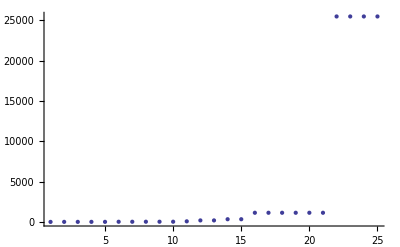

```mathematica
ListPlot[%]
```

```mathematica
RepeatDigits[10]
```

Found sufficient length at 15

Found repeating pattern after 39366

Count without a 2 in it 512

Bad positions {24, 26, 72, 126, 186, 240, 242, 332, 474, 560, 728, 774, 864, 872, 992, 1028, 1044, 1046, 1134, 1190, 1260, 1460, 1478, 1482, 1644, 1646, 1676, 1698, 1700, 1844, 1878, 1932, 1946, 2006, 2130, 2184, 2186, 2202, 2322, 2330, 2450, 2454, 2456, 2486, 2580, 2904, 2936, 3132, 3248, 3294, 3314, 3336, 3402, 3464, 3482, 3564, 3566, 3746, 3800, 4038, 4076, 4106, 4232, 4376, 4382, 4538, 4706, 4752, 4934, 5102, 5246, 5256, 5366, 5562, 5564, 5604, 5748, 5832, 5834, 5888, 5958, 6018, 6228, 6306, 6326, 6380, 6444, 6504, 6560, 6576, 6704, 6720, 6824, 6830, 6866, 6876, 6966, 7092, 7136, 7316, 7346, 7362, 7370, 7506, 7686, 7688, 7776, 7838, 7962, 8034, 8064, 8120, 8178, 8450, 8520, 8664, 8682, 8828, 8912, 8934, 8936, 8966, 9134, 9222, 9236, 9384, 9396, 9522, 9612, 9630, 9776, 9936, 10140, 10206, 10226, 10262, 10422, 10424, 10448, 10692, 10694, 10700, 10842, 11090, 11240, 11252, 11466, 11510, 11522, 11690, 11720, 11744, 12042, 12230, 12276, 12390, 12546, 12548, 12552, 12660, 12852, 12854, 12894, 12980, 13038, 13110, 13122, 13124, 13130, 13146, 13194, 13202, 13248, 13310, 13340, 13362, 13454, 13508, 13610, 13688, 13772, 14114, 14150, 14166, 14256, 14352, 14382, 14496, 14514, 14588, 14600, 14604, 14706, 14796, 14798, 14820, 14822, 14976, 14978, 15000, 15066, 15068, 15140, 15216, 15306, 15308, 15410, 15444, 15452, 15464, 15468, 15576, 15578, 15624, 15626, 15702, 15714, 15896, 16026, 16202, 16436, 16458, 16586, 16604, 16650, 16686, 16812, 16868, 16920, 16922, 17036, 17160, 17198, 17226, 17228, 17354, 17430, 17496, 17498, 17504, 17568, 17660, 17828, 17874, 17990, 18062, 18132, 18144, 18146, 18488, 18656, 18756, 18962, 18978, 19010, 19140, 19194, 19352, 19428, 19514, 19566, 19626, 19680, 19682, 19698, 19784, 19818, 19826, 19950, 19952, 19988, 20258, 20400, 20438, 20484, 20576, 20628, 20808, 20810, 20832, 20898, 20960, 21084, 21138, 21156, 21242, 21408, 21410, 21446, 21534, 21572, 21716, 21858, 21894, 21896, 21950, 21996, 22034, 22056, 22058, 22088, 22110, 22112, 22248, 22256, 22344, 22358, 22364, 22644, 22734, 22752, 22914, 22916, 23004, 23030, 23058, 23328, 23384, 23516, 23714, 23748, 23940, 24212, 24356, 24362, 24374, 24450, 24588, 24632, 24644, 24806, 24812, 24858, 25118, 25164, 25182, 25434, 25436, 25458, 25530, 25674, 25820, 26016, 26090, 26160, 26270, 26324, 26430, 26432, 26462, 26486, 26630, 26718, 26732, 26804, 26810, 26894, 26972, 27018, 27108, 27116, 27290, 27434, 27474, 27618, 27636, 27704, 27710, 27828, 27888, 27890, 27918, 28088, 28098, 28100, 28176, 28188, 28250, 28262, 28338, 28374, 28446, 28532, 28586, 28590, 28694, 28730, 28746, 28748, 28836, 29018, 29180, 29324, 29376, 29492, 29538, 29646, 29772, 29810, 29934, 30042, 30158, 30348, 30552, 30618, 30690, 31112, 31178, 31184, 31254, 31266, 31268, 31346, 31490, 31500, 31778, 31806, 31808, 31848, 31878, 31992, 32076, 32078, 32084, 32100, 32202, 32316, 32472, 32474, 32570, 32624, 32636, 32802, 32906, 32940, 32964, 33068, 33072, 33120, 33210, 33336, 33522, 33590, 33614, 33698, 33954, 34260, 34308, 34422, 34530, 34532, 34568, 34656, 34764, 34838, 34908, 34926, 34980, 35016, 35018, 35118, 35232, 35234, 35370, 35486, 35628, 35640, 36020, 36036, 36038, 36126, 36152, 36384, 36470, 36638, 36666, 36668, 36692, 36836, 36870, 36936, 36938, 36944, 37062, 37086, 37478, 37572, 37928, 37964, 37980, 37988, 38240, 38304, 38474, 38520, 38556, 38558, 38580, 38634, 38652, 38790, 38792, 38904, 38942, 39096, 39098, 39212, 39224, 39354, 39366, 39368, 39374}

{24,26,72,126,186,240,242,332,474,560,728,774,864,872,992,1028,1044,1046,1134,1190,1260,1460,1478,1482,1644,1646,1676,1698,1700,1844,1878,1932,1946,2006,2130,2184,2186,2202,2322,2330,2450,2454,2456,2486,2580,2904,2936,3132,3248,3294,3314,3336,3402,3464,3482,3564,3566,3746,3800,4038,4076,4106,4232,4376,4382,4538,4706,4752,4934,5102,5246,5256,5366,5562,5564,5604,5748,5832,5834,5888,5958,6018,6228,6306,6326,6380,6444,6504,6560,6576,6704,6720,6824,6830,6866,6876,6966,7092,7136,7316,7346,7362,7370,7506,7686,7688,7776,7838,7962,8034,8064,8120,8178,8450,8520,8664,8682,8828,8912,8934,8936,8966,9134,9222,9236,9384,9396,9522,9612,9630,9776,9936,10140,10206,10226,10262,10422,10424,10448,10692,10694,10700,10842,11090,11240,11252,11466,11510,11522,11690,11720,11744,12042,12230,12276,12390,12546,12548,12552,12660,12852,12854,12894,12980,13038,13110,13122,13124,13130,13146,13194,13202,13248,13310,13340,13362,13454,13508,13610,13688,13772,14114,14150,14166,14256,14352,14382,14496,14514,14588,14600,14604,14706,14796,14798,14820,14822,14976,14978,15000,15066,15068,15140,15216,15306,15308,15410,15444,15452,15464,15468,15576,15578,15624,15626,15702,15714,15896,16026,16202,16436,16458,16586,16604,16650,16686,16812,16868,16920,16922,17036,17160,17198,17226,17228,17354,17430,17496,17498,17504,17568,17660,17828,17874,17990,18062,18132,18144,18146,18488,18656,18756,18962,18978,19010,19140,19194,19352,19428,19514,19566,19626,19680,19682,19698,19784,19818,19826,19950,19952,19988,20258,20400,20438,20484,20576,20628,20808,20810,20832,20898,20960,21084,21138,21156,21242,21408,21410,21446,21534,21572,21716,21858,21894,21896,21950,21996,22034,22056,22058,22088,22110,22112,22248,22256,22344,22358,22364,22644,22734,22752,22914,22916,23004,23030,23058,23328,23384,23516,23714,23748,23940,24212,24356,24362,24374,24450,24588,24632,24644,24806,24812,24858,25118,25164,25182,25434,25436,25458,25530,25674,25820,26016,26090,26160,26270,26324,26430,26432,26462,26486,26630,26718,26732,26804,26810,26894,26972,27018,27108,27116,27290,27434,27474,27618,27636,27704,27710,27828,27888,27890,27918,28088,28098,28100,28176,28188,28250,28262,28338,28374,28446,28532,28586,28590,28694,28730,28746,28748,28836,29018,29180,29324,29376,29492,29538,29646,29772,29810,29934,30042,30158,30348,30552,30618,30690,31112,31178,31184,31254,31266,31268,31346,31490,31500,31778,31806,31808,31848,31878,31992,32076,32078,32084,32100,32202,32316,32472,32474,32570,32624,32636,32802,32906,32940,32964,33068,33072,33120,33210,33336,33522,33590,33614,33698,33954,34260,34308,34422,34530,34532,34568,34656,34764,34838,34908,34926,34980,35016,35018,35118,35232,35234,35370,35486,35628,35640,36020,36036,36038,36126,36152,36384,36470,36638,36666,36668,36692,36836,36870,36936,36938,36944,37062,37086,37478,37572,37928,37964,37980,37988,38240,38304,38474,38520,38556,38558,38580,38634,38652,38790,38792,38904,38942,39096,39098,39212,39224,39354,39366,39368,39374}

```mathematica
N[Log[2,512]]
```

9.

```mathematica
N[9^Log[2,3]]
```

32.5416

```mathematica
AreGoodDigits[digits_]:=Module[{i},
For[i=1, i<=Length[digits], i++,
If [digits[[i]]> 1, Return[False]]
];
Return [True];
]
```

```mathematica
RepeatDigitsTail[p_,q_,n_]:= RepeatDigitsTail[p,q,n]=Module[{startPattern,  start = 0, current, digits, bad, tail, badList},
digits = IntegerDigits[p^start, q];
badList={};
While[Length[digits] < n,
start +=1;
digits = IntegerDigits[p^start, q];
];
startPattern = Take[digits,-n];
current = start +1;
digits = IntegerDigits[p^current, q];
tail = Take[digits,-n];
bad=0;
If [AreGoodDigits[tail], bad +=1; AppendTo[badList,current]];
Monitor[
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[p^current, q];
tail = Take[digits,-n];
If [AreGoodDigits[tail], bad +=1; AppendTo[badList,tail]];
],
current
];
Return[{n,start, current-start, bad}]
]
```

```mathematica
Clear[RepeatDigitsTail]
```

```mathematica
Monitor[Table[RepeatDigitsTail[3,5,i], {i,1,5}],i]
```

{{1,0,4,1},{2,2,20,2},{3,3,100,4},{4,5,500,8},{5,6,2500,16}}

```mathematica
2338/446
```

1169/223

```mathematica
Monitor[Table[RepeatDigitsTail[5,7,i], {i,1,6}],i]
```

{{1,0,6,1},{2,2,42,2},{3,3,294,4},{4,4,2058,8},{5,5,14406,16},{6,7,100842,32}}

```mathematica
Monitor[Table[RepeatDigitsTail[3,5,i], {i,1,7}],i]
```

{{1,0,4,1},{2,2,20,2},{3,3,100,4},{4,5,500,8},{5,6,2500,16},{6,8,12500,32},{7,9,62500,64}}

```mathematica
Monitor[Table[RepeatDigitsTail[2,3,i], {i,1,11}],i]
```

{{1,0,2,1},{2,2,6,2},{3,4,18,4},{4,5,54,8},{5,7,162,16},{6,8,486,32},{7,10,1458,64},{8,12,4374,128},{9,13,13122,256},{10,15,39366,512},{11,16,118098,1024}}

```mathematica
Monitor[Table[RepeatDigitsTail[2,5,i], {i,1,14}],i]
```

{{1,0,4,1},{2,3,20,2},{3,5,100,4},{4,7,500,8},{5,10,2500,16},{6,12,12500,32},{7,14,62500,64}}

```mathematica
Monitor[Table[RepeatDigitsTail[7,11,i], {i,1,5}],i]
```

{{1,0,10,1},{2,2,110,2},{3,3,1210,4},{4,4,13310,8},{5,5,146410,16}}

```mathematica
TableForm[Table[IntegerDigits[7^i,11],{i,0,10}], TableAlignments->Right]
```

1 |  |  |  |  |  |  |  | 
7 |  |  |  |  |  |  |  | 
4 | 5 |  |  |  |  |  |  | 
2 | 9 | 2 |  |  |  |  |  | 
1 | 8 | 9 | 3 |  |  |  |  | 
1 | 1 | 6 | 9 | 10 |  |  |  | 
8 | 0 | 4 | 3 | 4 |  |  |  | 
5 | 1 | 2 | 8 | 1 | 6 |  |  | 
3 | 2 | 8 | 8 | 1 | 10 | 9 |  | 
2 | 0 | 8 | 6 | 2 | 2 | 9 | 8 | 
1 | 3 | 5 | 4 | 10 | 4 | 9 | 2 | 1

```mathematica
Ratios[Monitor[Table[RepeatDigitsTail[5,7,i], {i,1,5}],i]]
```

Divide::infy: Infinite expression 2/0 encountered.

{{2,ComplexInfinity,7,2},{3/2,3/2,7,2},{4/3,4/3,7,2},{5/4,5/4,7,2}}

```mathematica
RepeatDigitsTailBis[p_,q_,n_]:= RepeatDigitsTailBis[p,q,n]=Module[{startPattern,  start = 0, current, digits,  tail,patternList},
digits = IntegerDigits[p^start, q];
patternList={};
While[Length[digits] < n,
start +=1;
digits = IntegerDigits[p^start, q];
];
startPattern = Take[digits,-n];
AppendTo[patternList,startPattern];
current = start +1;
digits = IntegerDigits[p^current, q];
tail = Take[digits,-n];
Monitor[
While[tail ≠ startPattern,
AppendTo[patternList,tail];
current +=1;
digits = IntegerDigits[p^current, q];
tail = Take[digits,-n];
],
current
];
Return[patternList]
]
```

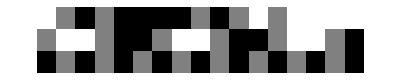

```mathematica
ArrayPlot[Transpose[RepeatDigitsTailBis[2,3,3]]]
```

```mathematica
Ratios[Table[Length[RepeatDigitsTailBis[2,3,i]],{i,1,10}]]
```

{5/2,17/5,53/17,162/53,3,3,3,3,3}

```mathematica
FindFit[Table[Length[RepeatDigitsTailBis[2,3,i]],{i,1,11}],2*3^(x-1)+c,{a,b,c},x]
```

```mathematica
SimpleDigitsTailBis[p_,q_,n_]:= SimpleDigitsTailBis[p,q,n]=Module[{startPattern,  start = 0, current, digits,  tail,patternList},
digits = IntegerDigits[start,p* q];
patternList={};
While[Length[digits] < n,
start +=1;
digits = IntegerDigits[start,p* q];
];
startPattern = Take[digits,-n];
current = start +1;
digits = IntegerDigits[current,p* q];
tail = Take[digits,-n];
Monitor[
While[tail ≠ startPattern,
AppendTo[patternList,tail];
current +=1;
digits = IntegerDigits[current,p* q];
tail = Take[digits,-n];
],
current
];
Return[patternList]
]
```

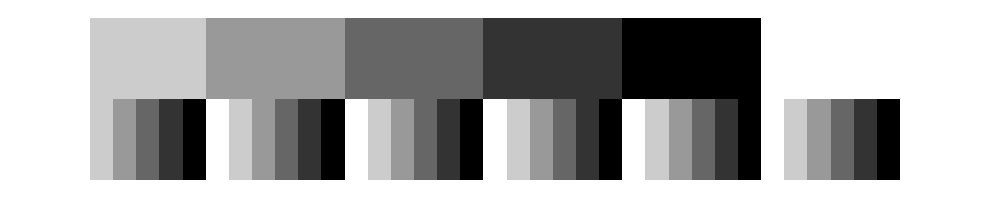

```mathematica
ArrayPlot[Transpose[SimpleDigitsTailBis[2,3,2]]]
```

```mathematica
RepeatDigits[n_]:=RepeatDigits[n]= Module[{startPattern,  start = 0, current, digits, bad, tail, badList, firstBad},
badList={};
digits = IntegerDigits[2^start, 3];
While[Length[digits] < n,
start +=1;
digits = IntegerDigits[2^start, 3];
];
Print["Found sufficient length at " <> ToString[start]];
startPattern = Take[digits,-n];
current = start +1;
digits = IntegerDigits[2^current, 3];
tail = Take[digits,-n];
bad=0;
firstBad=0;
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current];If[firstBad==0,firstBad=current]];
Monitor[
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[2^current, 3];
tail = Take[digits,-n];
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current];If[firstBad==0,firstBad=current]];
],
current];
Print["Found repeating pattern after " <> ToString[current- start]];
Print["Count without a 2 in it " <> ToString[bad]];
Print["Bad positions " <> ToString[badList]];
Return[{n,start->current,bad, firstBad}]
]
```

```mathematica
Table[RepeatDigits[i],{i,1,10}]
```

Found sufficient length at 0

Found repeating pattern after 2

Count without a 2 in it 1

Bad positions {2}

Found sufficient length at 2

Found repeating pattern after 6

Count without a 2 in it 2

Bad positions {6, 8}

Found sufficient length at 4

Found repeating pattern after 18

Count without a 2 in it 4

Bad positions {6, 8, 18, 20}

Found sufficient length at 5

Found repeating pattern after 54

Count without a 2 in it 8

Bad positions {8, 18, 20, 24, 26, 42, 54, 56}

Found sufficient length at 7

Found repeating pattern after 162

Count without a 2 in it 16

Bad positions {8, 20, 24, 26, 54, 56, 62, 72, 74, 78, 80, 96, 126, 150, 162, 164}

Found sufficient length at 8

Found repeating pattern after 486

Count without a 2 in it 32

Bad positions {20, 24, 26, 56, 62, 72, 74, 80, 126, 150, 162, 164, 186, 188, 216, 218, 240, 242, 258, 288, 332, 344, 378, 386, 396, 398, 402, 420, 474, 486, 488, 494}

Found sufficient length at 10

Found repeating pattern after 1458

Count without a 2 in it 64

Bad positions {20, 24, 26, 56, 72, 80, 126, 164, 186, 188, 216, 218, 240, 242, 332, 378, 386, 396, 398, 420, 474, 486, 488, 494, 548, 560, 566, 612, 636, 648, 650, 672, 726, 728, 744, 774, 830, 864, 872, 882, 884, 888, 992, 996, 998, 1028, 1034, 1044, 1046, 1122, 1134, 1160, 1188, 1190, 1230, 1260, 1304, 1316, 1374, 1392, 1446, 1458, 1460, 1466}

Found sufficient length at 12

Found repeating pattern after 4374

Count without a 2 in it 128

Bad positions {24, 26, 72, 80, 126, 164, 186, 188, 218, 240, 242, 332, 378, 386, 474, 488, 494, 560, 566, 636, 648, 650, 728, 774, 864, 872, 882, 992, 1028, 1044, 1046, 1134, 1160, 1188, 1190, 1230, 1260, 1374, 1392, 1458, 1460, 1466, 1478, 1482, 1514, 1584, 1644, 1646, 1674, 1676, 1698, 1700, 1844, 1854, 1856, 1878, 1932, 1944, 1946, 1952, 2006, 2018, 2070, 2094, 2130, 2184, 2186, 2202, 2288, 2322, 2330, 2342, 2346, 2450, 2454, 2456, 2486, 2492, 2502, 2504, 2580, 2592, 2718, 2762, 2774, 2904, 2936, 2942, 2972, 2988, 2996, 3080, 3132, 3248, 3294, 3312, 3314, 3336, 3402, 3464, 3482, 3528, 3564, 3566, 3588, 3642, 3660, 3690, 3746, 3798, 3800, 3804, 3912, 3914, 3950, 4038, 4076, 4104, 4106, 4146, 4220, 4232, 4290, 4308, 4362, 4374, 4376, 4382}

Found sufficient length at 13

Found repeating pattern after 13122

Count without a 2 in it 256

Bad positions {24, 26, 72, 80, 126, 186, 188, 218, 240, 242, 332, 386, 474, 488, 560, 566, 650, 728, 774, 864, 872, 992, 1028, 1044, 1046, 1134, 1190, 1230, 1260, 1374, 1392, 1460, 1466, 1478, 1482, 1584, 1644, 1646, 1674, 1676, 1698, 1700, 1844, 1854, 1856, 1878, 1932, 1944, 1946, 2006, 2018, 2094, 2130, 2184, 2186, 2202, 2288, 2322, 2330, 2342, 2346, 2450, 2454, 2456, 2486, 2502, 2504, 2580, 2592, 2774, 2904, 2936, 3080, 3132, 3248, 3294, 3314, 3336, 3402, 3464, 3482, 3528, 3564, 3566, 3690, 3746, 3798, 3800, 3914, 4038, 4076, 4104, 4106, 4232, 4308, 4374, 4376, 4382, 4446, 4538, 4706, 4752, 4868, 4934, 4940, 5010, 5022, 5024, 5102, 5246, 5256, 5366, 5534, 5562, 5564, 5604, 5634, 5748, 5832, 5834, 5840, 5856, 5888, 5958, 6018, 6072, 6228, 6230, 6306, 6326, 6380, 6392, 6444, 6504, 6558, 6560, 6576, 6662, 6696, 6704, 6720, 6824, 6828, 6830, 6866, 6876, 6966, 7092, 7136, 7278, 7316, 7346, 7362, 7370, 7454, 7506, 7686, 7688, 7710, 7776, 7838, 7962, 8016, 8034, 8064, 8120, 8178, 8286, 8288, 8324, 8412, 8450, 8520, 8594, 8664, 8682, 8736, 8772, 8774, 8828, 8874, 8912, 8934, 8936, 8966, 8988, 8990, 9126, 9134, 9222, 9236, 9242, 9384, 9396, 9522, 9612, 9630, 9776, 9792, 9794, 9882, 9908, 9936, 10140, 10206, 10226, 10262, 10394, 10422, 10424, 10448, 10592, 10626, 10692, 10694, 10700, 10818, 10842, 11090, 11234, 11240, 11252, 11328, 11466, 11510, 11522, 11684, 11690, 11720, 11736, 11744, 11996, 12042, 12060, 12230, 12276, 12312, 12314, 12336, 12390, 12408, 12546, 12548, 12552, 12660, 12698, 12852, 12854, 12894, 12968, 12980, 13038, 13110, 13122, 13124, 13130}

Found sufficient length at 15

Found repeating pattern after 39366

Count without a 2 in it 512

Bad positions {24, 26, 72, 126, 186, 240, 242, 332, 474, 560, 728, 774, 864, 872, 992, 1028, 1044, 1046, 1134, 1190, 1260, 1460, 1478, 1482, 1644, 1646, 1676, 1698, 1700, 1844, 1878, 1932, 1946, 2006, 2130, 2184, 2186, 2202, 2322, 2330, 2450, 2454, 2456, 2486, 2580, 2904, 2936, 3132, 3248, 3294, 3314, 3336, 3402, 3464, 3482, 3564, 3566, 3746, 3800, 4038, 4076, 4106, 4232, 4376, 4382, 4538, 4706, 4752, 4934, 5102, 5246, 5256, 5366, 5562, 5564, 5604, 5748, 5832, 5834, 5888, 5958, 6018, 6228, 6306, 6326, 6380, 6444, 6504, 6560, 6576, 6704, 6720, 6824, 6830, 6866, 6876, 6966, 7092, 7136, 7316, 7346, 7362, 7370, 7506, 7686, 7688, 7776, 7838, 7962, 8034, 8064, 8120, 8178, 8450, 8520, 8664, 8682, 8828, 8912, 8934, 8936, 8966, 9134, 9222, 9236, 9384, 9396, 9522, 9612, 9630, 9776, 9936, 10140, 10206, 10226, 10262, 10422, 10424, 10448, 10692, 10694, 10700, 10842, 11090, 11240, 11252, 11466, 11510, 11522, 11690, 11720, 11744, 12042, 12230, 12276, 12390, 12546, 12548, 12552, 12660, 12852, 12854, 12894, 12980, 13038, 13110, 13122, 13124, 13130, 13146, 13194, 13202, 13248, 13310, 13340, 13362, 13454, 13508, 13610, 13688, 13772, 14114, 14150, 14166, 14256, 14352, 14382, 14496, 14514, 14588, 14600, 14604, 14706, 14796, 14798, 14820, 14822, 14976, 14978, 15000, 15066, 15068, 15140, 15216, 15306, 15308, 15410, 15444, 15452, 15464, 15468, 15576, 15578, 15624, 15626, 15702, 15714, 15896, 16026, 16202, 16436, 16458, 16586, 16604, 16650, 16686, 16812, 16868, 16920, 16922, 17036, 17160, 17198, 17226, 17228, 17354, 17430, 17496, 17498, 17504, 17568, 17660, 17828, 17874, 17990, 18062, 18132, 18144, 18146, 18488, 18656, 18756, 18962, 18978, 19010, 19140, 19194, 19352, 19428, 19514, 19566, 19626, 19680, 19682, 19698, 19784, 19818, 19826, 19950, 19952, 19988, 20258, 20400, 20438, 20484, 20576, 20628, 20808, 20810, 20832, 20898, 20960, 21084, 21138, 21156, 21242, 21408, 21410, 21446, 21534, 21572, 21716, 21858, 21894, 21896, 21950, 21996, 22034, 22056, 22058, 22088, 22110, 22112, 22248, 22256, 22344, 22358, 22364, 22644, 22734, 22752, 22914, 22916, 23004, 23030, 23058, 23328, 23384, 23516, 23714, 23748, 23940, 24212, 24356, 24362, 24374, 24450, 24588, 24632, 24644, 24806, 24812, 24858, 25118, 25164, 25182, 25434, 25436, 25458, 25530, 25674, 25820, 26016, 26090, 26160, 26270, 26324, 26430, 26432, 26462, 26486, 26630, 26718, 26732, 26804, 26810, 26894, 26972, 27018, 27108, 27116, 27290, 27434, 27474, 27618, 27636, 27704, 27710, 27828, 27888, 27890, 27918, 28088, 28098, 28100, 28176, 28188, 28250, 28262, 28338, 28374, 28446, 28532, 28586, 28590, 28694, 28730, 28746, 28748, 28836, 29018, 29180, 29324, 29376, 29492, 29538, 29646, 29772, 29810, 29934, 30042, 30158, 30348, 30552, 30618, 30690, 31112, 31178, 31184, 31254, 31266, 31268, 31346, 31490, 31500, 31778, 31806, 31808, 31848, 31878, 31992, 32076, 32078, 32084, 32100, 32202, 32316, 32472, 32474, 32570, 32624, 32636, 32802, 32906, 32940, 32964, 33068, 33072, 33120, 33210, 33336, 33522, 33590, 33614, 33698, 33954, 34260, 34308, 34422, 34530, 34532, 34568, 34656, 34764, 34838, 34908, 34926, 34980, 35016, 35018, 35118, 35232, 35234, 35370, 35486, 35628, 35640, 36020, 36036, 36038, 36126, 36152, 36384, 36470, 36638, 36666, 36668, 36692, 36836, 36870, 36936, 36938, 36944, 37062, 37086, 37478, 37572, 37928, 37964, 37980, 37988, 38240, 38304, 38474, 38520, 38556, 38558, 38580, 38634, 38652, 38790, 38792, 38904, 38942, 39096, 39098, 39212, 39224, 39354, 39366, 39368, 39374}

{{1,0→2,1,2},{2,2→8,2,6},{3,4→22,4,6},{4,5→59,8,8},{5,7→169,16,8},{6,8→494,32,20},{7,10→1468,64,20},{8,12→4386,128,24},{9,13→13135,256,24},{10,15→39381,512,24}}

```mathematica
Clear[RepeatDigitsStart0]
```

```mathematica
Take[IntegerDigits[2^15,3],-10]
```

{1,1,2,2,2,2,1,1,2,2}

```mathematica
Take[IntegerDigits[2^39381,3],-10]
```

{1,1,2,2,2,2,1,1,2,2}

```mathematica
PadTake[list_,n_] := Take[PadLeft[list,n],-n]
```

```mathematica
PadTake[{1},4]
```

{0,0,0,1}

```mathematica
RepeatDigitsStart0[n_]:=RepeatDigitsStart0[n]= Module[{startPattern,  start = 0, current, digits, bad, tail, badList, firstBad},
badList={};
digits = IntegerDigits[2^start, 3];
startPattern = PadTake[digits,n];
current = start +1;
digits = IntegerDigits[2^current, 3];
tail = PadTake[digits,n];
bad=0;
firstBad=0;
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current];If[firstBad==0,firstBad=current]];
Monitor[
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[2^current, 3];
tail = PadTake[digits,n];
If [!MemberQ[tail,2], bad +=1; AppendTo[badList,current];If[firstBad==0,firstBad=current]];
],
current];
Print["Found repeating pattern after " <> ToString[current- start]];
Print["Count without a 2 in it " <> ToString[bad]];
Print["Bad positions " <> ToString[badList]];
Return[{n,start->current,bad, firstBad}]
]
```

```mathematica
Monitor[Table[RepeatDigitsStart0[i],{i,1,11}],{i,"i"}]
```

{{1,0→2,1,2},{2,0→6,2,2},{3,0→18,4,2},{4,0→54,8,2},{5,0→162,16,2},{6,0→486,32,2},{7,0→1458,64,2},{8,0→4374,128,2},{9,0→13122,256,2},{10,0→39366,512,2},{11,0→118098,1024,2}}

```mathematica
Map[#[[2]][[2]]&,%]
```

{2,6,18,54,162,486,1458,4374,13122,39366}

```mathematica
Table[EulerPhi[3^n],{n,1,20}]
```

{2,6,18,54,162,486,1458,4374,13122,39366,118098,354294,1062882,3188646,9565938,28697814,86093442,258280326,774840978,2324522934}

```mathematica
Table[Mod[2^(k*(2*3^(n))),3],{n,1,10},{k,1,10}]
```

{{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

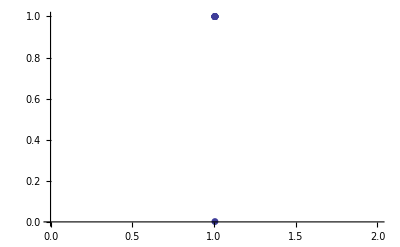

```mathematica
ListPlot[
Table[{1,Mod[2^EulerPhi[3^k],3^k]},{k,0,10}],PlotMarkers->Automatic]
```

```mathematica
Monitor[Table[Mod[q^n,p^k]-Mod[q^(n+EulerPhi[p^k]),p^k],{n,1,20},{k,1,5},{p,Prime[Range[2,2]]},{q,Prime[Range[3,10]]}],{p,q,k,n}]
```

{{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}},{{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0}}}}

```mathematica
2^n≡3^k Mod 2^(3^k+n)
```

```mathematica
Mod[Congruent[2^n,2^(n+EulerPhi[3^k])],3^k]
```

```mathematica
(2^n≡2^(3^k+n))3^k
```

```mathematica
FullSimplify[Mod[Congruent[2^n,2^(n+EulerPhi[3^k])],3^k]]
```

Mod[2^n≡2^(n+EulerPhi[3^k]),3^k]

```mathematica
Mod[p^n ≡ p^(EulerPhi[q^k] + n), q^k]
```

```mathematica
(p^n≡p^(q^k+n))q^k
```

```mathematica
EulerPhi[3]
```

2

```mathematica
3^6(1-1/3)
```

486

```mathematica
FullSimplify[Mod[2^n,3^k]-Mod[2^(n+3^k(1-1/3)),3^k]]
```

Mod[2^n,3^k]-Mod[2^(2 3^(-1+k)+n),3^k]

```mathematica
Clear[RepeatDigitsStart0]
```

```mathematica
RepeatDigitsStart0[n_]:=Module[{startPattern,  start = 0, current, digits, bad, tail, badList, firstBad, residueList={}},
badList={};
digits = IntegerDigits[2^start, 3];
startPattern = PadTake[digits,n];
current = start +1;
digits = IntegerDigits[2^current, 3];
tail = PadTake[digits,n];
bad=0;
firstBad=0;
If [!MemberQ[tail,2], 
bad +=1; AppendTo[badList,current];If[firstBad==0,firstBad=current];
AppendTo[residueList,Style[FromDigits[tail,3], Bold, Underlined]],
AppendTo[residueList,FromDigits[tail,3]]];
Monitor[
While[tail ≠ startPattern,
current +=1;
digits = IntegerDigits[2^current, 3];
tail = PadTake[digits,n];
If [!MemberQ[tail,2], 
bad +=1; AppendTo[badList,current];If[firstBad==0,firstBad=current];
AppendTo[residueList,Style[FromDigits[tail,3], Bold,Underlined]],
AppendTo[residueList,FromDigits[tail,3]]];
],
current];
Print["Found repeating pattern after " <> ToString[current- start]];
Print["Count without a 2 in it " <> ToString[bad]];
Print["Bad positions " <> ToString[badList]];
Return[{n,start->current,bad, firstBad, residueList}]
]
```

```mathematica
Export["c:\\temp\\exp.rtf",Table[Last[RepeatDigitsStart0[i]],{i,1,7}],"RTF"]
```

Found repeating pattern after 2

Count without a 2 in it 1

Bad positions {2}

Found repeating pattern after 6

Count without a 2 in it 2

Bad positions {2, 6}

Found repeating pattern after 18

Count without a 2 in it 4

Bad positions {2, 6, 8, 18}

Found repeating pattern after 54

Count without a 2 in it 8

Bad positions {2, 8, 18, 20, 24, 26, 42, 54}

Found repeating pattern after 162

Count without a 2 in it 16

Bad positions {2, 8, 20, 24, 26, 54, 56, 62, 72, 74, 78, 80, 96, 126, 150, 162}

Found repeating pattern after 486

Count without a 2 in it 32

Bad positions {2, 8, 20, 24, 26, 56, 62, 72, 74, 80, 126, 150, 162, 164, 186, 188, 216, 218, 240, 242, 258, 288, 332, 344, 378, 386, 396, 398, 402, 420, 474, 486}

Found repeating pattern after 1458

Count without a 2 in it 64

Bad positions {2, 8, 20, 24, 26, 56, 72, 80, 126, 164, 186, 188, 216, 218, 240, 242, 332, 378, 386, 396, 398, 420, 474, 486, 488, 494, 548, 560, 566, 612, 636, 648, 650, 672, 726, 728, 744, 774, 830, 864, 872, 882, 884, 888, 992, 996, 998, 1028, 1034, 1044, 1046, 1122, 1134, 1160, 1188, 1190, 1230, 1260, 1304, 1316, 1374, 1392, 1446, 1458}

c:\temp\exp.rtf

```mathematica
Table[Last[RepeatDigitsStart0[i]],{i,1,10}]
```

Found repeating pattern after 2

Count without a 2 in it 1

Bad positions {2}

Found repeating pattern after 6

Count without a 2 in it 2

Bad positions {2, 6}

Found repeating pattern after 18

Count without a 2 in it 4

Bad positions {2, 6, 8, 18}

Found repeating pattern after 54

Count without a 2 in it 8

Bad positions {2, 8, 18, 20, 24, 26, 42, 54}

Found repeating pattern after 162

Count without a 2 in it 16

Bad positions {2, 8, 20, 24, 26, 54, 56, 62, 72, 74, 78, 80, 96, 126, 150, 162}

Found repeating pattern after 486

Count without a 2 in it 32

Bad positions {2, 8, 20, 24, 26, 56, 62, 72, 74, 80, 126, 150, 162, 164, 186, 188, 216, 218, 240, 242, 258, 288, 332, 344, 378, 386, 396, 398, 402, 420, 474, 486}

Found repeating pattern after 1458

Count without a 2 in it 64

Bad positions {2, 8, 20, 24, 26, 56, 72, 80, 126, 164, 186, 188, 216, 218, 240, 242, 332, 378, 386, 396, 398, 420, 474, 486, 488, 494, 548, 560, 566, 612, 636, 648, 650, 672, 726, 728, 744, 774, 830, 864, 872, 882, 884, 888, 992, 996, 998, 1028, 1034, 1044, 1046, 1122, 1134, 1160, 1188, 1190, 1230, 1260, 1304, 1316, 1374, 1392, 1446, 1458}

Found repeating pattern after 4374

Count without a 2 in it 128

Bad positions {2, 8, 24, 26, 72, 80, 126, 164, 186, 188, 218, 240, 242, 332, 378, 386, 474, 488, 494, 560, 566, 636, 648, 650, 728, 774, 864, 872, 882, 992, 1028, 1044, 1046, 1134, 1160, 1188, 1190, 1230, 1260, 1374, 1392, 1458, 1460, 1466, 1478, 1482, 1514, 1584, 1644, 1646, 1674, 1676, 1698, 1700, 1844, 1854, 1856, 1878, 1932, 1944, 1946, 1952, 2006, 2018, 2070, 2094, 2130, 2184, 2186, 2202, 2288, 2322, 2330, 2342, 2346, 2450, 2454, 2456, 2486, 2492, 2502, 2504, 2580, 2592, 2718, 2762, 2774, 2904, 2936, 2942, 2972, 2988, 2996, 3080, 3132, 3248, 3294, 3312, 3314, 3336, 3402, 3464, 3482, 3528, 3564, 3566, 3588, 3642, 3660, 3690, 3746, 3798, 3800, 3804, 3912, 3914, 3950, 4038, 4076, 4104, 4106, 4146, 4220, 4232, 4290, 4308, 4362, 4374}

Found repeating pattern after 13122

Count without a 2 in it 256

Bad positions {2, 8, 24, 26, 72, 80, 126, 186, 188, 218, 240, 242, 332, 386, 474, 488, 560, 566, 650, 728, 774, 864, 872, 992, 1028, 1044, 1046, 1134, 1190, 1230, 1260, 1374, 1392, 1460, 1466, 1478, 1482, 1584, 1644, 1646, 1674, 1676, 1698, 1700, 1844, 1854, 1856, 1878, 1932, 1944, 1946, 2006, 2018, 2094, 2130, 2184, 2186, 2202, 2288, 2322, 2330, 2342, 2346, 2450, 2454, 2456, 2486, 2502, 2504, 2580, 2592, 2774, 2904, 2936, 3080, 3132, 3248, 3294, 3314, 3336, 3402, 3464, 3482, 3528, 3564, 3566, 3690, 3746, 3798, 3800, 3914, 4038, 4076, 4104, 4106, 4232, 4308, 4374, 4376, 4382, 4446, 4538, 4706, 4752, 4868, 4934, 4940, 5010, 5022, 5024, 5102, 5246, 5256, 5366, 5534, 5562, 5564, 5604, 5634, 5748, 5832, 5834, 5840, 5856, 5888, 5958, 6018, 6072, 6228, 6230, 6306, 6326, 6380, 6392, 6444, 6504, 6558, 6560, 6576, 6662, 6696, 6704, 6720, 6824, 6828, 6830, 6866, 6876, 6966, 7092, 7136, 7278, 7316, 7346, 7362, 7370, 7454, 7506, 7686, 7688, 7710, 7776, 7838, 7962, 8016, 8034, 8064, 8120, 8178, 8286, 8288, 8324, 8412, 8450, 8520, 8594, 8664, 8682, 8736, 8772, 8774, 8828, 8874, 8912, 8934, 8936, 8966, 8988, 8990, 9126, 9134, 9222, 9236, 9242, 9384, 9396, 9522, 9612, 9630, 9776, 9792, 9794, 9882, 9908, 9936, 10140, 10206, 10226, 10262, 10394, 10422, 10424, 10448, 10592, 10626, 10692, 10694, 10700, 10818, 10842, 11090, 11234, 11240, 11252, 11328, 11466, 11510, 11522, 11684, 11690, 11720, 11736, 11744, 11996, 12042, 12060, 12230, 12276, 12312, 12314, 12336, 12390, 12408, 12546, 12548, 12552, 12660, 12698, 12852, 12854, 12894, 12968, 12980, 13038, 13110, 13122}

Found repeating pattern after 39366

Count without a 2 in it 512

Bad positions {2, 8, 24, 26, 72, 126, 186, 240, 242, 332, 474, 560, 728, 774, 864, 872, 992, 1028, 1044, 1046, 1134, 1190, 1260, 1460, 1478, 1482, 1644, 1646, 1676, 1698, 1700, 1844, 1878, 1932, 1946, 2006, 2130, 2184, 2186, 2202, 2322, 2330, 2450, 2454, 2456, 2486, 2580, 2904, 2936, 3132, 3248, 3294, 3314, 3336, 3402, 3464, 3482, 3564, 3566, 3746, 3800, 4038, 4076, 4106, 4232, 4376, 4382, 4538, 4706, 4752, 4934, 5102, 5246, 5256, 5366, 5562, 5564, 5604, 5748, 5832, 5834, 5888, 5958, 6018, 6228, 6306, 6326, 6380, 6444, 6504, 6560, 6576, 6704, 6720, 6824, 6830, 6866, 6876, 6966, 7092, 7136, 7316, 7346, 7362, 7370, 7506, 7686, 7688, 7776, 7838, 7962, 8034, 8064, 8120, 8178, 8450, 8520, 8664, 8682, 8828, 8912, 8934, 8936, 8966, 9134, 9222, 9236, 9384, 9396, 9522, 9612, 9630, 9776, 9936, 10140, 10206, 10226, 10262, 10422, 10424, 10448, 10692, 10694, 10700, 10842, 11090, 11240, 11252, 11466, 11510, 11522, 11690, 11720, 11744, 12042, 12230, 12276, 12390, 12546, 12548, 12552, 12660, 12852, 12854, 12894, 12980, 13038, 13110, 13122, 13124, 13130, 13146, 13194, 13202, 13248, 13310, 13340, 13362, 13454, 13508, 13610, 13688, 13772, 14114, 14150, 14166, 14256, 14352, 14382, 14496, 14514, 14588, 14600, 14604, 14706, 14796, 14798, 14820, 14822, 14976, 14978, 15000, 15066, 15068, 15140, 15216, 15306, 15308, 15410, 15444, 15452, 15464, 15468, 15576, 15578, 15624, 15626, 15702, 15714, 15896, 16026, 16202, 16436, 16458, 16586, 16604, 16650, 16686, 16812, 16868, 16920, 16922, 17036, 17160, 17198, 17226, 17228, 17354, 17430, 17496, 17498, 17504, 17568, 17660, 17828, 17874, 17990, 18062, 18132, 18144, 18146, 18488, 18656, 18756, 18962, 18978, 19010, 19140, 19194, 19352, 19428, 19514, 19566, 19626, 19680, 19682, 19698, 19784, 19818, 19826, 19950, 19952, 19988, 20258, 20400, 20438, 20484, 20576, 20628, 20808, 20810, 20832, 20898, 20960, 21084, 21138, 21156, 21242, 21408, 21410, 21446, 21534, 21572, 21716, 21858, 21894, 21896, 21950, 21996, 22034, 22056, 22058, 22088, 22110, 22112, 22248, 22256, 22344, 22358, 22364, 22644, 22734, 22752, 22914, 22916, 23004, 23030, 23058, 23328, 23384, 23516, 23714, 23748, 23940, 24212, 24356, 24362, 24374, 24450, 24588, 24632, 24644, 24806, 24812, 24858, 25118, 25164, 25182, 25434, 25436, 25458, 25530, 25674, 25820, 26016, 26090, 26160, 26270, 26324, 26430, 26432, 26462, 26486, 26630, 26718, 26732, 26804, 26810, 26894, 26972, 27018, 27108, 27116, 27290, 27434, 27474, 27618, 27636, 27704, 27710, 27828, 27888, 27890, 27918, 28088, 28098, 28100, 28176, 28188, 28250, 28262, 28338, 28374, 28446, 28532, 28586, 28590, 28694, 28730, 28746, 28748, 28836, 29018, 29180, 29324, 29376, 29492, 29538, 29646, 29772, 29810, 29934, 30042, 30158, 30348, 30552, 30618, 30690, 31112, 31178, 31184, 31254, 31266, 31268, 31346, 31490, 31500, 31778, 31806, 31808, 31848, 31878, 31992, 32076, 32078, 32084, 32100, 32202, 32316, 32472, 32474, 32570, 32624, 32636, 32802, 32906, 32940, 32964, 33068, 33072, 33120, 33210, 33336, 33522, 33590, 33614, 33698, 33954, 34260, 34308, 34422, 34530, 34532, 34568, 34656, 34764, 34838, 34908, 34926, 34980, 35016, 35018, 35118, 35232, 35234, 35370, 35486, 35628, 35640, 36020, 36036, 36038, 36126, 36152, 36384, 36470, 36638, 36666, 36668, 36692, 36836, 36870, 36936, 36938, 36944, 37062, 37086, 37478, 37572, 37928, 37964, 37980, 37988, 38240, 38304, 38474, 38520, 38556, 38558, 38580, 38634, 38652, 38790, 38792, 38904, 38942, 39096, 39098, 39212, 39224, 39354, 39366}

{{2,1},«8»,{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,6487,12974,25948,51896,44743,30437,1825,3650,7300,14600,29200,58400,57751,56453,53857,48665,38281,17513,35026,11003,22006,44012,28975,57950,56851,«39286»,1988,3976,7952,15904,31808,4567,9134,18268,36536,14023,28046,56092,53135,47221,35393,11737,23474,46948,34847,10645,21290,42580,26111,52222,45395,31741,4433,8866,17732,35464,11879,23758,47516,35983,12917,25834,51668,44287,29525,1}}

```mathematica
Select[{2,4,8,16,32,64,128,256,512,1024,2048,1909,1631,1075,2150,2113,2039,1891,1595,1003,2006,1825,1463,739,1478,769,1538,889,1778,1369,551,1102,17,34,68,136,272,544,1088,2176,2165,2143,2099,2011,1835,1483,779,1558,929,1858,1529,871,1742,1297,407,814,1628,1069,2138,2089,1991,1795,1403,619,1238,289,578,1156,125,250,500,1000,2000,1813,1439,691,1382,577,1154,121,242,484,968,1936,1685,1183,179,358,716,1432,677,1354,521,1042,2084,1981,1775,1363,539,1078,2156,2125,2063,1939,1691,1195,203,406,812,1624,1061,2122,2057,1927,1667,1147,107,214,428,856,1712,1237,287,574,1148,109,218,436,872,1744,1301,415,830,1660,1133,79,158,316,632,1264,341,682,1364,541,1082,2164,2141,2095,2003,1819,1451,715,1430,673,1346,505,1010,2020,1853,1519,851,1702,1217,247,494,988,1976,1765,1343,499,998,1996,1805,1423,659,1318,449,898,1796,1405,623,1246,305,610,1220,253,506,1012,2024,1861,1535,883,1766,1345,503,1006,2012,1837,1487,787,1574,961,1922,1657,1127,67,134,268,536,1072,2144,2101,2015,1843,1499,811,1622,1057,2114,2041,1895,1603,1019,2038,1889,1591,995,1990,1793,1399,611,1222,257,514,1028,2056,1925,1663,1139,91,182,364,728,1456,725,1450,713,1426,665,1330,473,946,1892,1597,1007,2014,1841,1495,803,1606,1025,2050,1913,1639,1091,2182,2177,2167,2147,2107,2027,1867,1547,907,1814,1441,695,1390,593,1186,185,370,740,1480,773,1546,905,1810,1433,679,1358,529,1058,2116,2045,1903,1619,1051,2102,2017,1847,1507,827,1654,1121,55,110,220,440,880,1760,1333,479,958,1916,1645,1103,19,38,76,152,304,608,1216,245,490,980,1960,1733,1279,371,742,1484,781,1562,937,1874,1561,935,1870,1553,919,1838,1489,791,1582,977,1954,1721,1255,323,646,1292,397,794,1588,989,1978,1769,1351,515,1030,2060,1933,1679,1171,155,310,620,1240,293,586,1172,157,314,628,1256,325,650,1300,413,826,1652,1117,47,94,188,376,752,1504,821,1642,1097,7,14,28,56,112,224,448,896,1792,1397,607,1214,241,482,964,1928,1669,1151,115,230,460,920,1840,1493,799,1598,1009,2018,1849,1511,835,1670,1153,119,238,476,952,1904,1621,1055,2110,2033,1879,1571,955,1910,1633,1079,2158,2129,2071,1955,1723,1259,331,662,1324,461,922,1844,1501,815,1630,1073,2146,2105,2023,1859,1531,875,1750,1313,439,878,1756,1325,463,926,1852,1517,847,1694,1201,215,430,860,1720,1253,319,638,1276,365,730,1460,733,1466,745,1490,793,1586,985,1970,1753,1319,451,902,1804,1421,655,1310,433,866,1732,1277,367,734,1468,749,1498,809,1618,1049,2098,2009,1831,1475,763,1526,865,1730,1273,359,718,1436,685,1370,553,1106,25,50,100,200,400,800,1600,1013,2026,1865,1543,899,1798,1409,631,1262,337,674,1348,509,1018,2036,1885,1583,979,1958,1729,1271,355,710,1420,653,1306,425,850,1700,1213,239,478,956,1912,1637,1087,2174,2161,2135,2083,1979,1771,1355,523,1046,2092,1997,1807,1427,667,1334,481,962,1924,1661,1135,83,166,332,664,1328,469,938,1876,1565,943,1886,1585,983,1966,1745,1303,419,838,1676,1165,143,286,572,1144,101,202,404,808,1616,1045,2090,1993,1799,1411,635,1270,353,706,1412,637,1274,361,722,1444,701,1402,617,1234,281,562,1124,61,122,244,488,976,1952,1717,1247,307,614,1228,269,538,1076,2152,2117,2047,1907,1627,1067,2134,2081,1975,1763,1339,491,982,1964,1741,1295,403,806,1612,1037,2074,1961,1735,1283,379,758,1516,845,1690,1193,199,398,796,1592,997,1994,1801,1415,643,1286,385,770,1540,893,1786,1385,583,1166,145,290,580,1160,133,266,532,1064,2128,2069,1951,1715,1243,299,598,1196,205,410,820,1640,1093,2186,2185,2183,2179,2171,2155,2123,2059,1931,1675,1163,139,278,556,1112,37,74,148,296,592,1184,181,362,724,1448,709,1418,649,1298,409,818,1636,1085,2170,2153,2119,2051,1915,1643,1099,11,22,44,88,176,352,704,1408,629,1258,329,658,1316,445,890,1780,1373,559,1118,49,98,196,392,784,1568,949,1898,1609,1031,2062,1937,1687,1187,187,374,748,1496,805,1610,1033,2066,1945,1703,1219,251,502,1004,2008,1829,1471,755,1510,833,1666,1145,103,206,412,824,1648,1109,31,62,124,248,496,992,1984,1781,1375,563,1126,65,130,260,520,1040,2080,1973,1759,1331,475,950,1900,1613,1039,2078,1969,1751,1315,443,886,1772,1357,527,1054,2108,2029,1871,1555,923,1846,1505,823,1646,1105,23,46,92,184,368,736,1472,757,1514,841,1682,1177,167,334,668,1336,485,970,1940,1693,1199,211,422,844,1688,1189,191,382,764,1528,869,1738,1289,391,782,1564,941,1882,1577,967,1934,1681,1175,163,326,652,1304,421,842,1684,1181,175,350,700,1400,613,1226,265,530,1060,2120,2053,1919,1651,1115,43,86,172,344,688,1376,565,1130,73,146,292,584,1168,149,298,596,1192,197,394,788,1576,965,1930,1673,1159,131,262,524,1048,2096,2005,1823,1459,731,1462,737,1474,761,1522,857,1714,1241,295,590,1180,173,346,692,1384,581,1162,137,274,548,1096,5,10,20,40,80,160,320,640,1280,373,746,1492,797,1594,1001,2002,1817,1447,707,1414,641,1282,377,754,1508,829,1658,1129,71,142,284,568,1136,85,170,340,680,1360,533,1066,2132,2077,1967,1747,1307,427,854,1708,1229,271,542,1084,2168,2149,2111,2035,1883,1579,971,1942,1697,1207,227,454,908,1816,1445,703,1406,625,1250,313,626,1252,317,634,1268,349,698,1396,605,1210,233,466,932,1864,1541,895,1790,1393,599,1198,209,418,836,1672,1157,127,254,508,1016,2032,1877,1567,947,1894,1601,1015,2030,1873,1559,931,1862,1537,887,1774,1361,535,1070,2140,2093,1999,1811,1435,683,1366,545,1090,2180,2173,2159,2131,2075,1963,1739,1291,395,790,1580,973,1946,1705,1223,259,518,1036,2072,1957,1727,1267,347,694,1388,589,1178,169,338,676,1352,517,1034,2068,1949,1711,1235,283,566,1132,77,154,308,616,1232,277,554,1108,29,58,116,232,464,928,1856,1525,863,1726,1265,343,686,1372,557,1114,41,82,164,328,656,1312,437,874,1748,1309,431,862,1724,1261,335,670,1340,493,986,1972,1757,1327,467,934,1868,1549,911,1822,1457,727,1454,721,1442,697,1394,601,1202,217,434,868,1736,1285,383,766,1532,877,1754,1321,455,910,1820,1453,719,1438,689,1378,569,1138,89,178,356,712,1424,661,1322,457,914,1828,1469,751,1502,817,1634,1081,2162,2137,2087,1987,1787,1387,587,1174,161,322,644,1288,389,778,1556,925,1850,1513,839,1678,1169,151,302,604,1208,229,458,916,1832,1477,767,1534,881,1762,1337,487,974,1948,1709,1231,275,550,1100,13,26,52,104,208,416,832,1664,1141,95,190,380,760,1520,853,1706,1225,263,526,1052,2104,2021,1855,1523,859,1718,1249,311,622,1244,301,602,1204,221,442,884,1768,1349,511,1022,2044,1901,1615,1043,2086,1985,1783,1379,571,1142,97,194,388,776,1552,917,1834,1481,775,1550,913,1826,1465,743,1486,785,1570,953,1906,1625,1063,2126,2065,1943,1699,1211,235,470,940,1880,1573,959,1918,1649,1111,35,70,140,280,560,1120,53,106,212,424,848,1696,1205,223,446,892,1784,1381,575,1150,113,226,452,904,1808,1429,671,1342,497,994,1988,1789,1391,595,1190,193,386,772,1544,901,1802,1417,647,1294,401,802,1604,1021,2042,1897,1607,1027,2054,1921,1655,1123,59,118,236,472,944,1888,1589,991,1982,1777,1367,547,1094,1},Length[#]==0&]
```

{2,8,16,32,64,128,512,1024,2048,1909,1631,1075,2150,2113,2039,1891,1595,2006,1825,1463,1478,1538,889,1778,1369,551,1102,17,34,68,136,272,544,1088,2176,2165,2143,2099,2011,1835,1483,779,1558,929,1858,1529,871,1742,1297,407,1628,1069,2138,2089,1991,1795,1403,619,1238,289,578,1156,125,250,500,2000,1813,1439,691,1382,577,1154,242,484,968,1936,1685,1183,179,358,716,1432,677,1354,521,1042,2084,1981,1775,1363,539,1078,2156,2125,2063,1939,1691,1195,203,406,812,1624,1061,2122,2057,1927,1667,1147,107,214,428,856,1712,1237,287,574,1148,218,436,872,1744,1301,415,830,1660,1133,79,158,316,632,1264,341,682,1364,541,1082,2164,2141,2095,2003,1819,1451,715,1430,673,1346,505,1010,2020,1853,1519,851,1702,1217,494,988,1976,1765,1343,499,998,1996,1805,1423,659,1318,449,898,1796,1405,623,1246,305,610,1220,506,2024,1861,1535,883,1766,1345,503,1006,2012,1837,1487,787,1574,961,1922,1657,1127,67,134,268,536,1072,2144,2101,2015,1843,1499,1622,2114,2041,1895,1603,1019,2038,1889,1591,995,1990,1793,1399,611,1222,257,514,1028,2056,1925,1663,1139,182,728,1456,725,1450,713,1426,665,1330,473,946,1892,1597,1007,2014,1841,1495,803,1606,1025,2050,1913,1639,1091,2182,2177,2167,2147,2107,2027,1867,1547,907,1814,1441,695,1390,593,1186,185,370,740,1480,773,1546,905,1810,1433,679,1358,529,1058,2116,2045,1903,1619,1051,2102,2017,1847,1507,827,1654,1121,55,110,220,440,880,1760,1333,479,958,1916,1645,1103,19,38,76,152,304,608,1216,245,490,980,1960,1733,1279,371,1484,781,1562,937,1874,1561,935,1870,1553,919,1838,1489,791,1582,977,1954,1721,1255,323,646,1292,397,794,1588,989,1978,1769,1351,515,1030,2060,1933,1679,1171,155,310,620,1240,293,586,1172,157,314,628,1256,650,1300,413,826,1652,1117,47,188,376,752,1504,821,1642,1097,7,14,56,224,448,896,1792,1397,607,1214,241,482,964,1928,1669,1151,115,230,460,920,1840,1493,799,1598,2018,1849,1511,835,1670,1153,119,238,476,952,1904,1621,1055,2110,2033,1879,1571,955,1910,1633,1079,2158,2129,2071,1955,1723,1259,331,662,1324,461,922,1844,1501,815,1630,1073,2146,2105,2023,1859,1531,875,1750,1313,439,878,1756,1325,463,926,1852,1517,1694,1201,215,430,860,1720,1253,319,638,1276,365,1460,1466,745,1490,793,1586,1970,1753,1319,451,902,1804,1421,655,1310,433,866,1732,1277,367,734,1468,749,1498,809,1618,1049,2098,2009,1831,1475,763,1526,865,1730,1273,359,718,1436,685,1370,553,1106,25,50,100,200,400,800,1600,1013,2026,1865,1543,899,1798,1409,631,1262,674,1348,509,1018,2036,1885,1583,979,1958,1729,1271,710,1420,653,1306,425,1700,1213,239,478,956,1912,1637,1087,2174,2161,2135,2083,1979,1771,1355,523,1046,2092,1997,1807,1427,667,1334,481,962,1924,1661,1135,83,166,332,664,1328,469,938,1876,1565,943,1886,1585,983,1966,1745,1303,419,1676,1165,143,286,572,1144,101,202,404,808,1616,1045,2090,1993,1799,1411,635,1270,353,706,1412,637,1274,722,1444,701,1402,617,1234,281,562,1124,61,122,488,1952,1717,1247,307,614,1228,269,538,1076,2152,2117,2047,1907,1627,1067,2134,2081,1975,1763,1339,491,1964,1741,1295,403,806,1612,1037,2074,1961,1735,1283,379,758,1516,845,1690,1193,199,398,796,1592,997,1994,1801,1415,643,1286,385,770,1540,893,1786,1385,583,1166,145,290,580,1160,133,266,532,1064,2128,2069,1951,1715,1243,299,598,1196,205,410,1640,2186,2185,2183,2179,2171,2155,2123,2059,1931,1675,1163,139,278,556,1112,74,148,296,592,1184,181,362,724,1448,709,1418,649,1298,409,818,1636,1085,2170,2153,2119,2051,1915,1643,1099,11,22,44,88,176,704,1408,629,1258,329,658,1316,445,890,1780,1373,559,1118,49,98,196,392,784,1568,949,1898,1609,1031,2062,1937,1687,1187,187,374,748,1496,805,1610,1033,2066,1945,1703,1219,251,502,1004,2008,1829,1471,755,1510,833,1666,1145,103,206,412,824,1648,1109,62,124,248,496,992,1984,1781,1375,563,1126,65,130,260,520,1040,2080,1973,1759,1331,475,950,1900,1613,1039,2078,1969,1751,1315,443,886,1772,1357,527,2108,2029,1871,1555,923,1846,1505,1646,1105,23,46,92,184,368,736,1472,1514,1682,1177,167,668,1336,485,970,1940,1693,1199,211,422,844,1688,1189,191,382,764,1528,869,1738,1289,391,782,1564,941,1882,1577,967,1934,1681,1175,163,326,652,1304,421,842,1684,1181,175,350,700,1400,613,1226,265,530,1060,2120,2053,1919,1651,1115,43,86,172,344,688,1376,565,1130,73,146,292,584,1168,149,298,596,1192,197,394,788,1576,965,1930,1673,1159,131,262,524,1048,2096,2005,1823,1459,731,1462,737,1474,761,1522,857,1714,1241,295,590,1180,173,346,692,1384,581,1162,137,548,1096,5,20,80,160,320,640,1280,373,746,1492,797,1594,1001,2002,1817,1447,707,1414,641,1282,377,754,1508,829,1658,1129,71,142,284,568,1136,170,340,680,1360,533,2132,2077,1967,1747,1307,427,854,1708,1229,542,2168,2149,2111,2035,1883,1579,971,1942,1697,1207,227,454,908,1816,1445,703,1406,625,1250,313,626,1252,317,634,1268,349,698,1396,605,1210,233,466,932,1864,1541,895,1790,1393,599,1198,209,418,836,1672,1157,127,254,508,1016,2032,1877,1567,947,1894,1601,1015,2030,1873,1559,931,1862,1537,887,1774,1361,535,1070,2140,2093,1999,1811,1435,683,1366,545,2180,2173,2159,2131,2075,1963,1739,1291,395,790,1580,1946,1705,1223,259,518,1036,2072,1957,1727,1267,347,694,1388,589,1178,169,338,676,1352,517,1034,2068,1949,1711,1235,566,1132,77,154,308,616,1232,277,554,1108,29,58,116,232,464,928,1856,1525,863,1726,1265,343,686,1372,557,1114,41,164,656,1312,437,874,1748,1309,431,862,1724,1261,335,670,1340,493,986,1972,1757,1327,467,934,1868,1549,911,1822,1457,727,1454,721,1442,697,1394,601,1202,217,434,868,1736,1285,383,1532,877,1754,1321,455,910,1820,1453,719,1438,689,1378,569,1138,89,178,356,712,1424,661,1322,457,914,1828,1469,751,1502,817,1634,2162,2137,2087,1987,1787,1387,587,1174,161,322,644,1288,389,778,1556,925,1850,1513,839,1678,1169,151,302,604,1208,229,458,916,1832,1477,767,1534,881,1762,1337,487,974,1948,1709,1231,275,550,1100,26,52,104,208,416,832,1664,1141,95,190,380,1520,853,1706,1225,263,526,1052,2104,2021,1855,1523,859,1718,1249,311,622,1244,301,602,1204,221,442,884,1768,1349,511,1022,2044,1901,1615,1043,2086,1985,1783,1379,571,1142,97,194,388,776,1552,917,1834,1481,775,1550,913,1826,1465,743,1486,785,1570,953,1906,1625,2126,2065,1943,1699,1211,235,470,940,1880,1573,959,1918,1649,1111,35,70,140,560,1120,53,106,212,424,848,1696,1205,223,446,892,1784,1381,575,1150,113,226,452,904,1808,1429,671,1342,497,994,1988,1789,1391,595,1190,193,386,772,1544,901,1802,1417,647,1294,401,802,1604,1021,2042,1897,1607,1027,2054,1921,1655,1123,59,236,472,944,1888,1589,991,1982,1777,1367,547,1094}

```mathematica
Map[FromDigits[IntegerDigits[#,3],2]&,{4,256,1003,739,769,814,1000,121,109,247,253,1012,811,1057,91,364,742,325,94,28,112,1009,847,730,733,985,337,355,850,838,361,244,976,982,820,1093,37,352,31,1054,823,757,841,334,274,10,40,85,1066,271,1084,1090,973,283,82,328,766,1081,13,760,1063,280,118,1}]
```

{3,39,107,69,79,83,105,31,25,35,37,111,81,115,21,63,71,49,23,9,27,109,93,65,67,103,55,59,95,89,61,33,99,101,85,127,13,57,11,113,87,73,91,53,43,5,15,19,119,41,123,125,97,47,17,51,77,121,7,75,117,45,29,1}

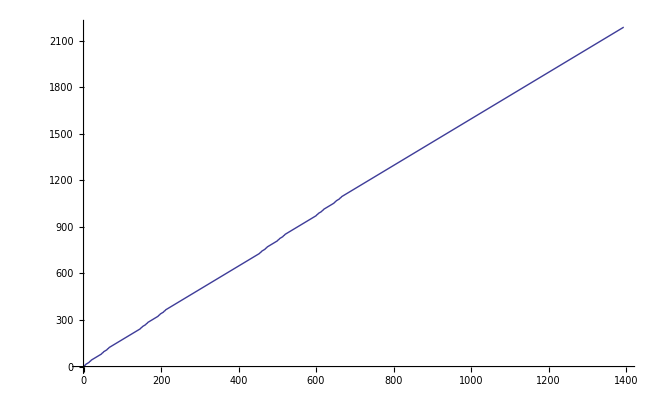

```mathematica
ListLinePlot[Sort[Out[168]]]
```

```mathematica
Module[{MAX=1500000,pow,three=3,current,last},
last = 0;
Monitor[
For [pow = 0, pow < 50, pow ++,
three=3^pow;
For[last=last,last≤MAX,last++,
If[IntegerLength[2^last,3]≥ pow, Break[]]
];
For[current=last, current ≤ MAX, current ++,
If[DigitCount[Mod[2^current,three],3,2] ==0, 
Print[{pow, last,current}];
last=current;
Break[];
];
];
If[current≥ MAX, Break[]];
],
{pow,last,current}
]
]
```

{0,0,0}

{1,0,0}

{2,2,2}

{3,4,6}

{4,6,8}

{5,8,8}

{6,8,8}

{7,10,20}

{8,20,24}

{9,24,24}

{10,24,24}

{11,24,72}

{12,72,186}

{13,186,186}

{14,186,332}

{15,332,332}

{16,332,1134}

{17,1134,1134}

{18,1134,1134}

{19,1134,1134}

{20,1134,1134}

{21,1134,1134}

{22,1134,25458}

{23,25458,25458}

{24,25458,25458}

{25,25458,25458}

{26,25458,25458}

{27,25458,25458}

{28,25458,159140}

{29,159140,249968}

{30,249968,249968}

{31,249968,249968}

{32,249968,249968}

{33,249968,249968}

{34,249968,249968}

{35,249968,249968}

{36,249968,249968}

```mathematica
Module[{MAX=1500000,val,pow,three=3,current,last,newPow},
last = 9;
pow=0;
Monitor[
While[pow≤MAX && last ≤ MAX,
three=3^pow;
For[current=last, current ≤ MAX, current ++,
val =2^current;
If[DigitCount[Mod[val,three],3,2] ==0, 
Print["Found : " <> ToString[current]];
last=current;
newPow =IntegerLength[val,3]; 
If[newPow==pow,
Print["Same power found"];
pow= pow +1
,
pow=IntegerLength[val,3];
];
Print["Going to power : " <> ToString[pow]];
Break[];
];
];
If[current≥ MAX, Break[]];
],
{pow,last,current}
]
]
```

Found : 9

Going to power : 6

Found : 20

Going to power : 13

Found : 186

Going to power : 118

$Aborted

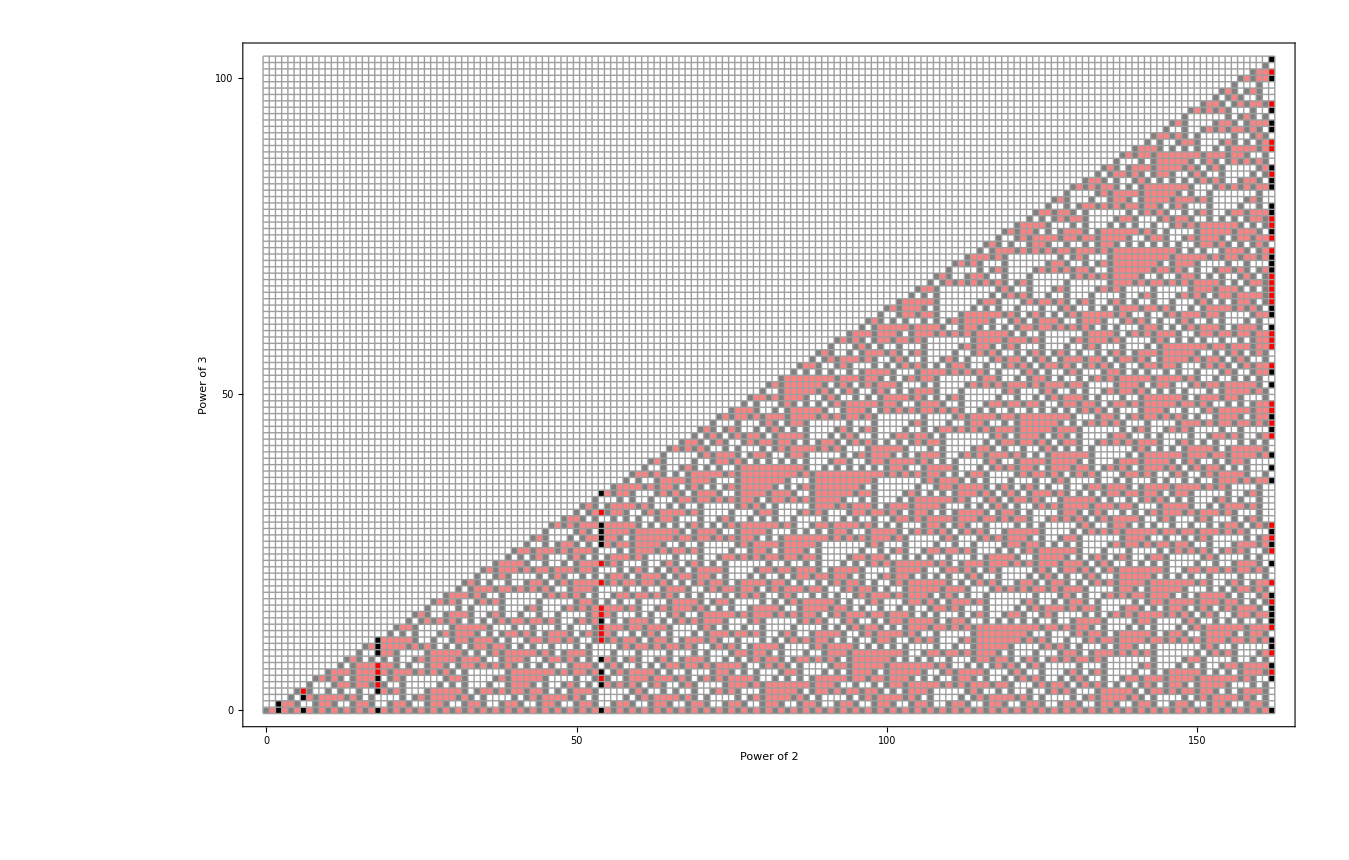

```mathematica
Module[
{max=2*3^4, max3},
max3=IntegerPart[Ceiling[max*Log[3,2]]];
ArrayPlot[Transpose[Table[
With[{keep=PadLeft[IntegerDigits[2^n,3],max3]},
If[IntegerQ[Log[3,n/2]], keep+3,keep]
],{n,0,max}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Gray,2->Pink,3->White,4->Black,5->Red}, DataRange->{{0,max},{0,max3}},FrameLabel->{"Power of 3", "Power of 2"} ]
]
```

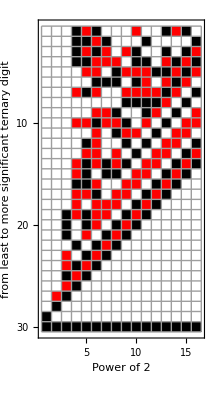

```mathematica
Module[
{ max3=15},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[2^(2*3^i),3],max3*2],max3*2]},
keep
],{i,0,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"from least to more significant ternary digit", "Power of 2"} ]
,i]
]
```

```mathematica
IntegerLength[2^(2*3^(18-1))]
```

77750126

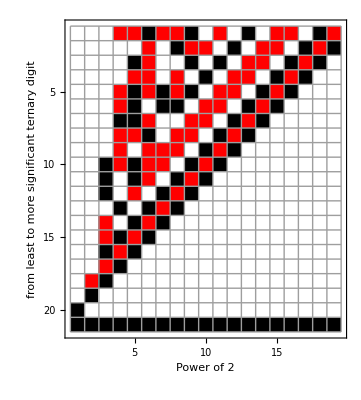

```mathematica
Module[
{ max3=18},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(2*3^i),3^(max3+3)],3],max3+3],max3+3]},
keep
],{i,0,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"from least to more significant ternary digit", "Power of 2"} ]
,i]
]
```

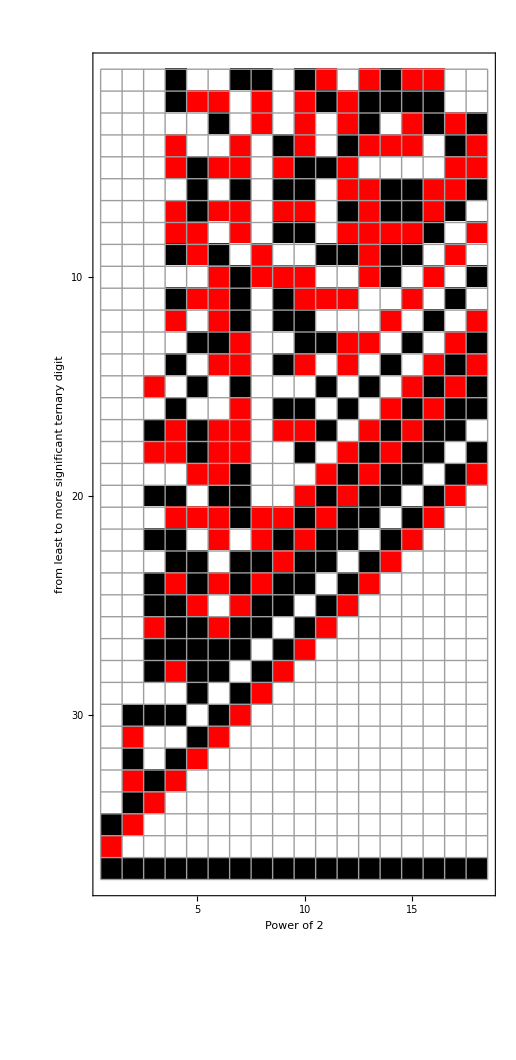

```mathematica
Module[
{ max3=17},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(4*3^i),3^(max3*2+3)],3],2*max3+3],2*max3+3]},
keep
],{i,0,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"from least to more significant ternary digit", "Power of 2"} ]
,i]
]
```

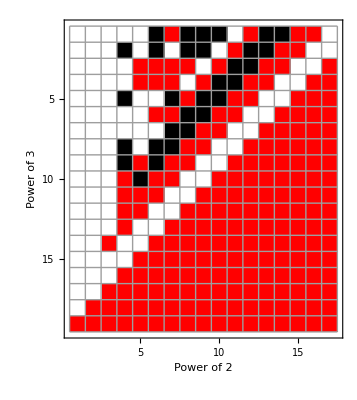

```mathematica
Module[
{ max3=16},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(3^i),3^(max3+3)],3],max3+3],max3+3]},
keep
],{i,0,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"Power of 3", "Power of 2"} ]
,i]
]
```

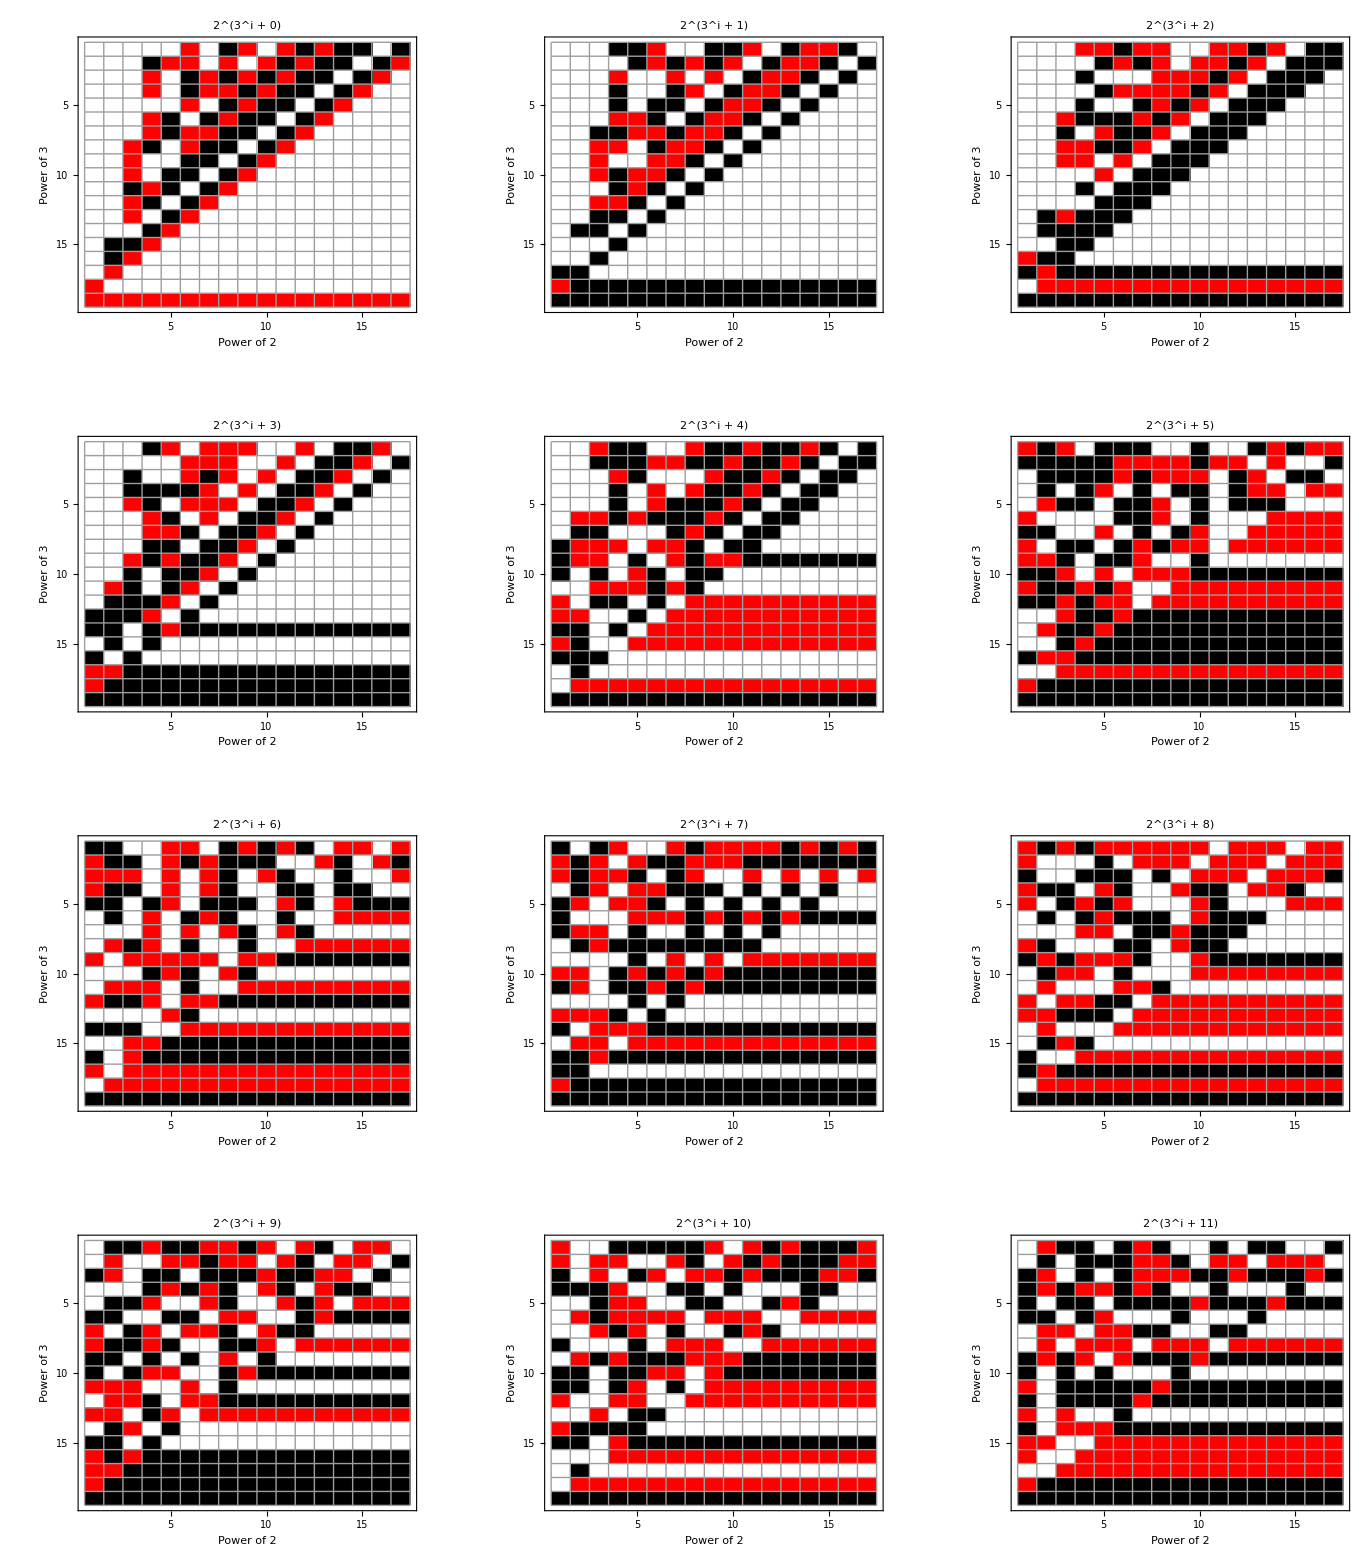

```mathematica
Module[
{ max3=16},
Monitor[
GraphicsArray[
Table[
Table[
ArrayPlot[
Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(2*3^i+2^plus),3^(max3+3)],3],max3+3],max3+3]},
keep
],{i,0,max3}]], 
Frame->True, 
FrameTicks->Automatic, 
Mesh->All, 
ColorRules->{0->White,1->Black,2->Red},
FrameLabel->{"Power of 3", "Power of 2"} ,
PlotLabel->"2^(3^i + " <> ToString[plus] <> ")"
],
{plus,row*3,(row+1)*3-1}
],
{row,0,3}
]
]
,{i,plus}]
]
```